```mathematica
Solve[p/(1-p)==1/d^2,p]
```

{{p→1/(1+d^2)}}

```mathematica
getc[n_, m_]:=m/Integrate[1/2 n^2/((u-v)^2+1),{u,0,1},{v,0,1}]
```

```mathematica
Integrate[1/(1+s^2),{s,-x,0}]+Integrate[1/(1+s^2),{s,0,1-x}]
```

ArcTan[1-x]+ArcTan[x]

```mathematica
c=1; n=1;
```

```mathematica
k[x_]:=If[0≤x≤ 1,c n (ArcTan[1-x]+ArcTan[x])];
```

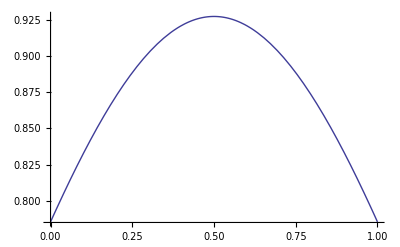

```mathematica
Plot[k[x],{x,0,1}]
```

```mathematica
kbounds={k[0.0],k[.5]}
```

{0.785398,0.927295}

```mathematica
x=InverseFunction[k[N[#]]&];
```

```mathematica
bigN[k_]:=n x'[k]
```